Qn 1)

```mathematica
Clear[a]
F = u*(1-u^s)-a*u
```

-a u+u (1-u^s)

Get the equilibria

```mathematica
Solve[F==0,u]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{u→0},{u→(1-a)^(1/s)}}

{{u→0},{u→(1-a)^(1/s)}}
u^*_0=0, u^*_1=(1-a)^(1/s)

```mathematica
DF=Simplify[D[F,u]]
```

-1-(1+s) u^s

```mathematica
-1-(1+s) u^s
print(F)
```

-1-(1+s) u^s

print (-2 u+u (1-u^s))

Stability analysis

2^(1/s)

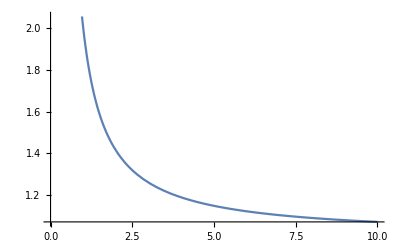

```mathematica
eq1=(2)^(1/s)
Plot[{eq1},{s,0,10}]
```

0.5^(1/s)

General::munfl: 0.5^4895.1 is too small to represent as a normalized machine number; precision may be lost.

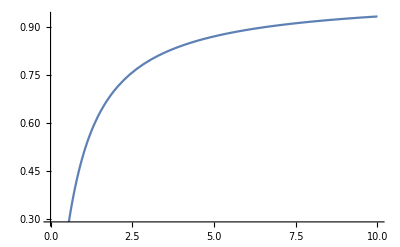

```mathematica
eq1=(.5)^(1/s)
Plot[{eq1},{s,0,10}]
```

```mathematica
DF=Simplify[D[F,u]]
```

1-a-(1+s) u^s

```mathematica
Simplify[DF/.{u->0}]
```

1-a-0^s (1+s)

Yield y=q*E*N(t)

```mathematica
F=q*e*(K*((1-((q*e)/r))^(1/s)));
DF=Simplify[D[F,e]];
Solve[DF==0,e]
```

{{e→(r s)/(q (1+s))}}

Qn 2)

```mathematica
CountRoots[1-x+(Exp[x-.6])/(1+Exp[x-.6]),{x,0,Infinity}]
```

1

```mathematica
CountRoots[.347-.9*x+(5*Exp[x-1.64])/(6+Exp[x-1.64]),{x,0,Infinity}]
```

3

```mathematica
CountRoots[.347-.9*x+(5*Exp[x-1.67])/(6+Exp[x-1.64]),{x,0,Infinity}]
```

1

```mathematica
CountRoots[1.1-.7*x+(4.4*Exp[x-1.67])/(1.7+Exp[x-3.65]),{x,0,Infinity}]
```

1

```mathematica
CountRoots[1.1-.7*x+(4.4*Exp[x-1.67])/(1.7+Exp[x-3.84]),{x,0,Infinity}]
```

1

```mathematica
CountRoots[.03-.6*x+(100*Exp[x-5])/(1.7+Exp[x-5]),{x,0,Infinity}]
```

1

Qn 3)

```mathematica
Plot[m^(0.1+1)/(1+m^(0.1)), {m,0,50}]
```

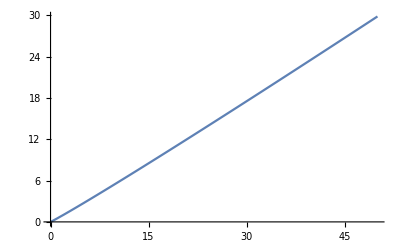

-Graphics-

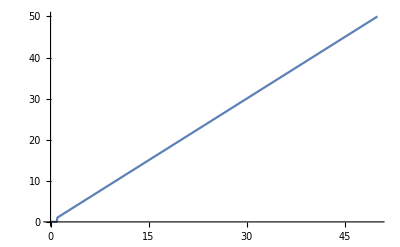

```mathematica
Plot[m^(60+1)/(1+m^(60)), {m,0,50}]
```